## Setup

```mathematica
Clear@Evaluate[Context[]<>"*"]
SetDirectory@NotebookDirectory[];
```

```mathematica
<<"Definitions/IO.wl"
<<"Definitions/Teukolsky.wl"
<<"Definitions/SWSH.wl"
```

## Equation and and Eigenvalue function

```mathematica
Eq=EqTeukolskyRadial/.RuleKRadial;
```

```mathematica
Clear@ℰ;
ℰ[𝓈_Integer,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real?Negative]:=ℰ[𝓈,ℓ,-𝓂,-𝒸];
ℰ[𝓈_Integer?Negative,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real]:=ℰ[-𝓈,ℓ,𝓂,𝒸];
ℰ[𝓈_Integer,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real]/;ℓ≥Max[Abs[𝓈],Abs[𝓂]]:=SpinWeightedSpheroidalHarmonicEigenvalue[𝓈,ℓ,𝓂,N@𝒸];
(*ℰ[𝓈_Integer,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real]/;ℓ≥Max[Abs[𝓈],Abs[𝓂]]:=(Simplify[SWSHEigenCoef//.Rule𝒽∪Ruleκpm∪{s->𝓈,m->𝓂}]/.l->ℓ).Table[𝒸^(i-1),{i,Length@SWSHEigenCoef}];*)
```

## Parameter rules and equation simplification

```mathematica
EquationF//Collect[#,{f''[x],f'[x],f[x]},FullSimplify]&
```

x f[x] (-(s+s^2+λ) (x+τ)-(ⅈ (x+τ+s τ) χ)/τ-((x+2 τ) χ^2)/τ^2+ω̄ (ⅈ s (2 x^2+2 τ+3 x τ)+2 (2+x) χ+x (2+x)^2 ω̄))+(x (x+τ) (τ (2 x+τ-s τ)-2 ⅈ (x+τ) χ) f'[x])/τ+x^2 (x+τ)^2 f''[x]

```mathematica
RuleRHorizon={R->Function[x,x^(-s-I χ/τ)f[x]]};
EquationF=PowerExpand@Simplify[x^(s+I χ/τ)x (x+τ) (Eq/.RuleRHorizon)];
(* all params *)
RuleBoundaryBH={𝒶[0]->1,𝒷[0]->(-ℬ τ^2)/(4 (ⅈ τ/2+χ) χ)};
RuleParams={τ->(2 √(1-𝒥^2))/(1+√(1-𝒥^2)),Ω̄->𝒥/2,χ->(ω̄-m Ω̄) (2-τ),rp->1+√(1-𝒥^2),ℬ->Sqrt[(λ+(s+1)s)^2-4((𝒥 ω̄)/rp)^2+4m (𝒥 ω̄)/rp],  
λ->((𝒥 ω̄)/rp)^2-2m((𝒥 ω̄)/rp)+ℰ[s,l,m,(𝒥 ω̄)/rp]-s(s+1)};
```

```mathematica
(* Function to replace all parameters accordingly *)
ReplaceParams[𝒿_,𝓈_,ℓ_,𝓂_]=#1//.RuleBoundaryBH∪RuleParams∪{s->𝓈,l->ℓ,m->𝓂,𝒥->𝒿}&;
ReplaceParams[𝒿_,𝓈_,ℓ_,𝓂_,𝓌_]=#1//.RuleBoundaryBH∪RuleParams∪{s->𝓈,l->ℓ,m->𝓂,𝒥->𝒿,ω̄->𝓌}&;
```

```mathematica
(* Coeficients to estimate f and f' close to BH horizon *)
nCoefH=6;
RuleFHorizon={f->Function[x,∑_(n=0)^nCoefH 𝒶[n] x^n]};
FSeriesCoefHorizon=First@Solve[CoefficientList[EquationF/.RuleFHorizon,x][[2;;nCoefH+1]]==0,Table[𝒶[n],{n,1,nCoefH}]//Evaluate];
```

```mathematica
(Simplify[(𝒶[1]/𝒶[0]/.FSeriesCoefHorizon)]//ReplaceParams[𝒿,-1,1,-1,0.4])/.{ℰ[__]->ℰ[-1,1,-1,0.4],√(1-𝒿^2)->0}//Simplify[(1-𝒿^2)#]/.𝒿->1&
```

0.+0.45 ⅈ

```mathematica
(* Coeficients to estimate Ain and Aout at infinity *)
nCoefInf=10;
RuleRinInf={R->Function[x,ⅇ^(-ⅈ ω̄ x)x^(-1-ⅈ ω̄ (2-τ)) ∑_(n=0)^nCoefInf 𝒾[n] x^-n]};
RuleRoutInf={R->Function[x, ⅇ^(ⅈ ω̄ x)x^(-1-2 s+ⅈ ω̄ (2-τ)) ∑_(n=0)^nCoefInf ℴ[n] x^-n]};
```

## Equation solver definition

```mathematica
(* OptionsPattern to use with SolveωF to get more precision/accuracy out of NDSolve *)
IncreasePrecision={PrecisionGoal->13,AccuracyGoal->70,MaxSteps->10^6};
```

#### Solver 1

```mathematica
(* Definition of the solver for s=1 and s=-1 equations using boundary conditions at BH horizon *)
Clear[SolveSingle];
SolveSingle[𝒿_?NumberQ,𝓈_?IntegerQ,ℓ_?IntegerQ,𝓂_?IntegerQ,{omega__?NumberQ},opts:OptionsPattern[]]/;0<𝒿<1&&Abs[𝓈]==1&&ℓ≥Max[Abs[𝓈],Abs[𝓂]]:=
Module[{eqF,delω,incs,fINF,k=0,last,olist,localk},
(* almost 0. starting point, BH horizon / almost ∞, a lot of wave lenghts way from horizon *)
x0=10^-12.;
xINF:=2 π/Abs[ω̄]*750.;

(* stuff to monitor asynchronously SolveωF using ParallelTable *)
SetSharedVariable[k];
ParallelEvaluate[last=AbsoluteTime[];localk=1];

(* using ReplaceParams once to save computation time *)
{eqF,delω,incs,fINF}=ReplaceParams[𝒿,𝓈,ℓ,𝓂][{EquationF,m Ω̄,({f[x0],f'[x0]}/.RuleFHorizon/.FSeriesCoefHorizon),f[xINF] ⅇ^(ⅈ(Sign[𝓈] ω̄ (xINF+(2-τ)Log[xINF])-χ/τ Log[xINF]))}];
olist=DeleteCases[{omega},(delω|0.|0)];
(* use Monitor ProgressIndicator with asynchronous refresh of the calculation state *)
Monitor[ParallelTable[
(* calculation state update with suppressed output *)
localk++;
If[AbsoluteTime[]-last>1,last=AbsoluteTime[];k+=localk;localk=0];

(* solving the equation using NDSolve and substituing the result *)
{𝒿,ω̄,fINF}/.First@NDSolve[{eqF==0,{f[x0],f'[x0]}==incs},f,{x,x0,xINF},Sequence@@FilterRules[{opts}, Options[NDSolve]]],{ω̄,olist}],
ProgressIndicator[k,{0,Length@olist}]]
];
```

#### Solver 2

```mathematica
Clear[SolveBoth];
SolveBoth[𝒿_?NumberQ,𝓈_?IntegerQ,ℓ_?IntegerQ,𝓂_?IntegerQ,𝓌_?NumberQ,opts:OptionsPattern[]]/;0<𝒿<1&&Abs[𝓈]==1&&ℓ≥Max[Abs[𝓈],Abs[𝓂]]:=
Module[{eqF,f0,fp0,coefInInf,coefOutInf,in,out,ev,x0,xINF},
(* almost 0. starting point, BH horizon / almost ∞, a lot of wave lenghts way from horizon *)
x0=10^-12.;
xINF=2Pi/Abs[𝓌]*80.;
ev=ℰ[𝓈,ℓ,𝓂,(𝒿 𝓌)/(1+Sqrt[1-𝒿^2])];
eqF=EquationF//ReplaceParams[𝒿,𝓈,l,𝓂,𝓌];

{f0,fp0}={f[x0],f'[x0]}/.RuleFHorizon/.First@Solve[CoefficientList[eqF/.RuleFHorizon,x][[2;;nCoefH+1]]==0,Table[𝒶[n],{n,1,nCoefH}]//Evaluate];
coefInInf=First@Solve[0==Simplify@SeriesCoefficient[Series[ⅇ^(ⅈ ω̄ x) x^(ⅈ ω̄ (2-τ)) Eq/.RuleRinInf,{x,∞,nCoefInf}]//ReplaceParams[𝒿,𝓈,l,𝓂,𝓌],#]&/@Range[nCoefInf],Evaluate@Table[𝒾[n],{n,1,nCoefInf}]];
coefOutInf=First@Solve[0==Simplify@SeriesCoefficient[Series[ⅇ^(-ⅈ ω̄ x) x^(2 s-ⅈ ω̄ (2-τ)) Eq/.RuleRoutInf,{x,∞,nCoefInf}]//ReplaceParams[𝒿,𝓈,l,𝓂,𝓌],#]&/@Range[nCoefInf],Evaluate@Table[ℴ[n],{n,1,nCoefInf}]];
{in,out}=Total@ReplaceParams[𝒿,𝓈,l,𝓂,𝓌][{R[x]/.RuleRinInf/.coefInInf,R[x]/.RuleRoutInf/.coefOutInf}]//{𝒾[0],ℴ[0]}/.First@Solve[{#==RInf,D[#,x]==RpInf}/.{x->xINF,ℰ[__]->ev},{𝒾[0],ℴ[0]}]&;
 
{𝒿,𝓌,in,out}/.ReplaceParams[𝒿,𝓈,l,𝓂,𝓌][{RInf->R[xINF],RpInf->R'[xINF]}/.RuleRHorizon]/.First@NDSolve[{eqF==0,f0==f[x0],fp0==f'[x0]}/.{ℰ[__]->ev,𝒶[0]->1},f,{x,x0,xINF},Sequence@@FilterRules[{opts}, Options[NDSolve]]]
];
```

## Analysis

### Large ℓ=40, varying 0<𝒿<1 and azimuthal number 𝓂

```mathematica
g=If[#>0,#-2Pi,#]&;
```

```mathematica
rng=Range[0.01,0.99,0.04]∪{0.98,0.99,0.999,0.9999};
```

```mathematica
test1=ParallelTable[ReplaceParams[𝒿,-1,40,1,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[𝒿,-1,40,1,0.4,IncreasePrecision],{𝒿,rng}];
```

```mathematica
test2=ParallelTable[ReplaceParams[𝒿,-1,40,0,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[𝒿,-1,40,0,0.4,IncreasePrecision],{𝒿,rng}];
```

```mathematica
test3=ParallelTable[ReplaceParams[𝒿,-1,40,-1,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[𝒿,-1,40,-1,0.4,IncreasePrecision],{𝒿,rng}];
```

```mathematica
test4=ParallelTable[ReplaceParams[𝒿,-1,40,7,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[𝒿,-1,40,7,0.4,IncreasePrecision],{𝒿,rng}];
```

FittedModel[-2.72831-(3.50601 x^2)/((1+√(1-x^2))^2)]

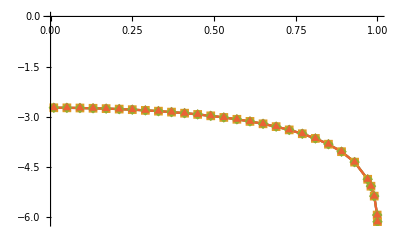

```mathematica
data1={rng[[#]],((Arg@test1[[#,3]]+If[Arg@test1[[#,3]]>0,-2Pi,0]))}&/@Range@Length@rng;
data2={rng[[#]],((Arg@test2[[#,3]]+If[Arg@test2[[#,3]]>0,-2Pi,0]))}&/@Range@Length@rng;
data3={rng[[#]],((Arg@test3[[#,3]]+If[Arg@test3[[#,3]]>0,-2Pi,0]))}&/@Range@Length@rng;
data4={rng[[#]],((Arg@test4[[#,3]]+If[Arg@test4[[#,3]]>0,-2Pi,0]))}&/@Range@Length@rng;
nlmf=NonlinearModelFit[data1,α+(β x^2)/(4(1+√(1-x^2))^2),{α,β,γ},x]
dataA={#,nlmf[#]}&/@rng;
{data1,data2,data3,data4}//ListPlot[#,Joined->True,PlotRange->All,PlotMarkers->Automatic]&
```

### Phases behaviour for |s|<ℓ<40

```mathematica
spin0=ParallelTable[ReplaceParams[j,-1,ℓ,1,0.4]@{j,l,1,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[j,-1,ℓ,1,0.4,{PrecisionGoal->13,AccuracyGoal->70,MaxSteps->10^8}],{j,0.01,0.96,0.05},{ℓ,30,30}]//Flatten[#,1]&;
```

```mathematica
spin1=ParallelTable[ReplaceParams[j,-1,ℓ,1,0.2]@{j,l,1,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[Echo@j,-1,ℓ,1,0.2,{PrecisionGoal->13,AccuracyGoal->70,MaxSteps->10^8}],{j,0.01,0.96,0.05},{ℓ,32,32}]//Flatten[#,1]&;
```

```mathematica
p1=ListPlot[{#1,g@Arg[#4]}&@@@spin0];
p3=ListPlot[{#1,g@Arg[#4]}&@@@spin1];
data0=ReplaceParams[#1,-1,30,1,0.4]@{#1,g@Arg[#4]-g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ) I ω̄]]}&@@@spin0;
p2=Plot[g@ReplaceParams[𝒿,-1,30,1,0.4][Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ) I ω̄]]-(-0(2-τ)ω̄+2(2-τ)ω̄ Log[2(2-τ)ω̄])],{𝒿,0,1},PlotStyle->Red];
p4=Plot[g@ReplaceParams[𝒿,-1,30,1,0.2][Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ) I ω̄]]-(+0(2-τ)ω̄+2(2-τ)ω̄ Log[2(2-τ)ω̄])],{𝒿,0,1},PlotStyle->Red];
Show[p1,p2,PlotRange->All]
Show[p3,p4,PlotRange->All]
```

```mathematica
modes1=ParallelTable[ReplaceParams[0.9,-1,ℓ,𝓂,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[0.9,-1,Echo@ℓ,𝓂,0.4,{PrecisionGoal->12,AccuracyGoal->60,MaxSteps->10^7}],{ℓ,1,50},{𝓂,{-1,0,1}}];
```

#### Fitting 1

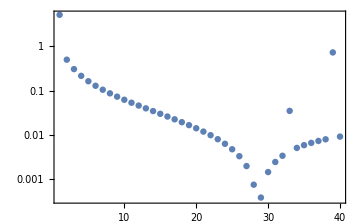
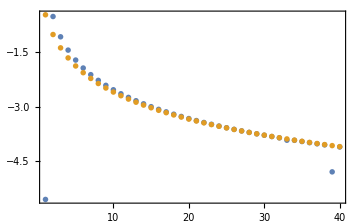
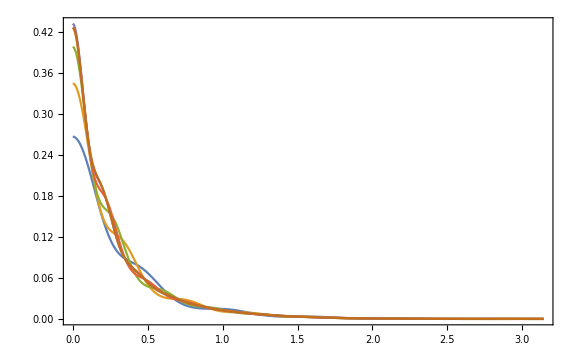
-Graphics- | -Graphics-
-Graphics- |

```mathematica
δ1=0.0265;
dataV1=Last[Flatten[modes1,{2}]]⟦;;40⟧;
funcV1=Table[#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[0.9,-1,ℓ,1,0.4]@(dataV1⟦ℓ,3⟧-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ1])SpinWeightedSphericalHarmonicY[-1,1,1,0,0]SpinWeightedSphericalHarmonicY[-1,ℓ,1,0,0]*SpinWeightedSphericalHarmonicY[-1,ℓ,1,θ,0],{ℓ,dataV1⟦All,1⟧}];
argV1={{#1,g@Arg@#3}&@@@dataV1,ReplaceParams[0.9,-1,#1,1,0.4]@{l,g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ1]]}&@@@dataV1}//ListPlot[#,Joined->False,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Medium]&;
diffV1=ReplaceParams[0.9,-1,#1,1,0.4]@{#1,g@Arg@#3-g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ1]]//Abs}&@@@dataV1//ListLogPlot[#,Joined->False,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Medium]&;
sumV1={Range[0,Pi,Pi/400],Abs[Total@funcV1[[1;;#]]]^2}ᵀ&/@{10,14,18,22,26,30}//ListPlot[#,Joined->True,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Large]&;
{{diffV1,argV1},{sumV1,SpanFromLeft}}//Grid
```

#### Fitting 2

```mathematica
modes2=ParallelTable[ReplaceParams[0.99,-1,ℓ,𝓂,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[0.99,-1,Echo@ℓ,𝓂,0.4,IncreasePrecision],{ℓ,1,50},{𝓂,{1}}];
```

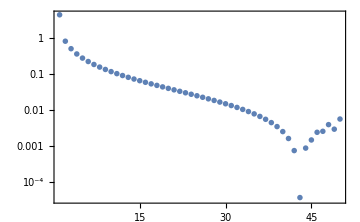
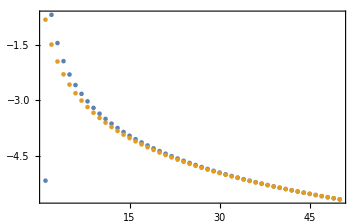
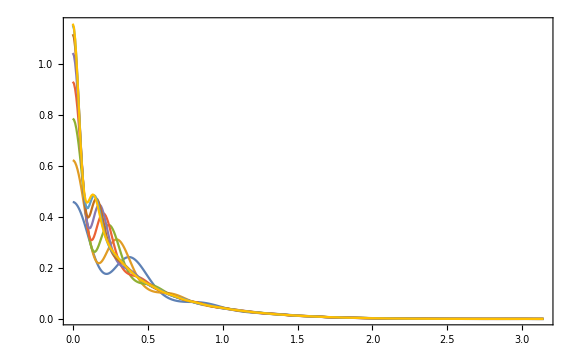
-Graphics- | -Graphics-
-Graphics- |

```mathematica
δ2=-0.18;
dataV2=Flatten[modes2,1][[;;50]];
funcV2=Table[#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[0.99,-1,ℓ,1,0.4]@(dataV2⟦ℓ,3⟧-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ2])SpinWeightedSphericalHarmonicY[-1,1,1,0,0]SpinWeightedSphericalHarmonicY[-1,ℓ,1,0,0]*SpinWeightedSphericalHarmonicY[-1,ℓ,1,θ,0],{ℓ,dataV2⟦All,1⟧}];
argV2={{#1,g@Arg@#3}&@@@dataV2,ReplaceParams[0.99,-1,#1,1,0.4]@{l,g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ2]]}&@@@dataV2}//ListPlot[#,Joined->False,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Medium]&;
diffV2=ReplaceParams[0.99,-1,#1,1,0.4]@{#1,g@Arg@#3-g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ2]]//Abs}&@@@dataV2//ListLogPlot[#,Joined->False,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Medium]&;
sumV2={Range[0,Pi,Pi/400],Abs[Total@funcV2[[1;;#]]]^2}ᵀ&/@{12,16,20,24,28,32,36,40}//ListPlot[#,Joined->True,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Large]&;
{{diffV2,argV2},{sumV2,SpanFromLeft}}//Grid
```

#### Fitting 3

```mathematica
modes3=ParallelTable[ReplaceParams[0.80,-1,ℓ,𝓂,0.3]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[0.80,-1,Echo@ℓ,𝓂,0.30,IncreasePrecision],{ℓ,1,50},{𝓂,{1}}];
```

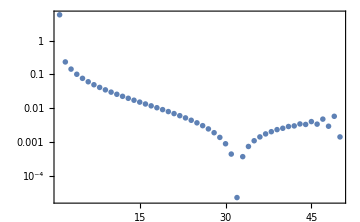
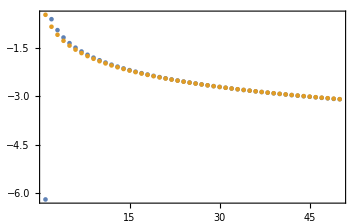
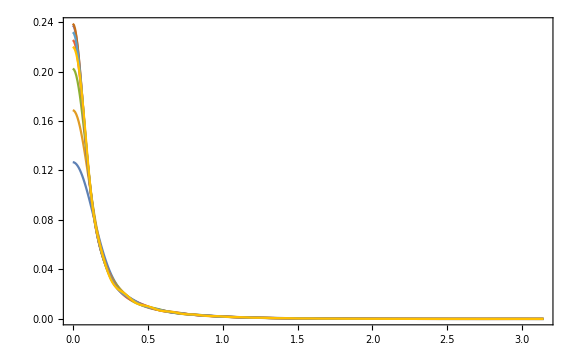
-Graphics- | -Graphics-
-Graphics- |

```mathematica
δ3=-0.145;
dataV3=Flatten[modes3,1];
funcV3=Table[#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[0.8,-1,ℓ,1,0.3]@(dataV3⟦ℓ,3⟧-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ3])SpinWeightedSphericalHarmonicY[-1,1,1,0,0]SpinWeightedSphericalHarmonicY[-1,ℓ,1,0,0]*SpinWeightedSphericalHarmonicY[-1,ℓ,1,θ,0],{ℓ,dataV3⟦All,1⟧}];
argV3={{#1,g@Arg@#3}&@@@dataV3,ReplaceParams[0.8,-1,#1,1,0.3]@{l,g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ3]]}&@@@dataV3}//ListPlot[#,Joined->False,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Medium]&;
diffV3=ReplaceParams[0.8,-1,#1,1,0.3]@{#1,g@Arg@#3-g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ3]]//Abs}&@@@dataV3//ListLogPlot[#,Joined->False,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Medium]&;
sumV3={Range[0,Pi,Pi/400],Abs[Total@funcV3[[1;;#]]]^2}ᵀ&/@{12,16,20,24,28,32,36,40}//ListPlot[#,Joined->True,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Large]&;
{{diffV3,argV3},{sumV3,SpanFromLeft}}//Grid
```

#### Fitting 4

```mathematica
modes4=ParallelTable[ReplaceParams[0.99,-1,ℓ,𝓂,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[0.99,-1,Sequence@@Echo[{ℓ,𝓂}],0.4,IncreasePrecision],{ℓ,1,40},{𝓂,-ℓ,ℓ}];
```

```mathematica
{0.99,0.4,#1,#2,Re@#3,Im@#3}&@@@Flatten[modes4,{1,2}]//Export["Zratio.csv",#]&
```

Zratio.csv

```mathematica
First/@dataV4[[All,All,1]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40}

```mathematica
Table[2l+1,{l,1,20}]//Accumulate//FindSequenceFunction
```

2 #1+#1^2&

```mathematica
δ4=-0.18;
dataV4=modes4;
{θ0,ϕ0}={0.3,0};
funcV4pos=ParallelTable[Total@#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[0.99,-1,ℓ,𝓂,0.4]@(dataV4⟦ℓ,ℓ+𝓂+1,3⟧-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ4])SpinWeightedSphericalHarmonicY[-1,1,-1,θ0,ϕ0]SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ0,ϕ0]*SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ,0],{ℓ,(First/@dataV4[[All,All,1]])},{𝓂,dataV4⟦ℓ,All,2⟧}];
funcV4neg=ParallelTable[Total@#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[0.99,-1,ℓ,𝓂,0.4]@(dataV4⟦ℓ,ℓ-𝓂+1,3⟧-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ4])SpinWeightedSphericalHarmonicY[-1,1,1,θ0,ϕ0]SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ0,ϕ0]*SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ,0],{ℓ,(First/@dataV4[[All,All,1]])},{𝓂,dataV4⟦ℓ,All,2⟧}];
```

```mathematica
funcV4pos0=ParallelTable[Total@#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[0.99,-1,ℓ,𝓂,0.4]@(dataV4⟦ℓ,ℓ+𝓂+1,3⟧-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ4])SpinWeightedSphericalHarmonicY[-1,1,1,θ0,ϕ0]SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ0,ϕ0]*SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ,0],{ℓ,(First/@dataV4[[All,All,1]])},{𝓂,dataV4⟦ℓ,All,2⟧}];
funcV4neg0=ParallelTable[Total@#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[0.99,-1,ℓ,𝓂,0.4]@(dataV4⟦ℓ,ℓ-𝓂+1,3⟧-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ4])SpinWeightedSphericalHarmonicY[-1,1,-1,θ0,ϕ0]SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ0,ϕ0]*SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ,0],{ℓ,(First/@dataV4[[All,All,1]])},{𝓂,dataV4⟦ℓ,All,2⟧}];
```

```mathematica
sumV4={Range[0,Pi,Pi/400],Abs[Total@funcV4pos[[1;;#]]]^2+Abs[Total@funcV4neg[[1;;#]]]^2}ᵀ&/@{40}//ListPlot[#,Joined->True,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Large]&;
sumV40={Range[0,Pi,Pi/400],Abs[Total@funcV4pos0[[1;;#]]]^2+Abs[Total@funcV4neg0[[1;;#]]]^2}ᵀ&/@{40}//ListPlot[#,Joined->True,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Large,PlotStyle->Red]&;
```

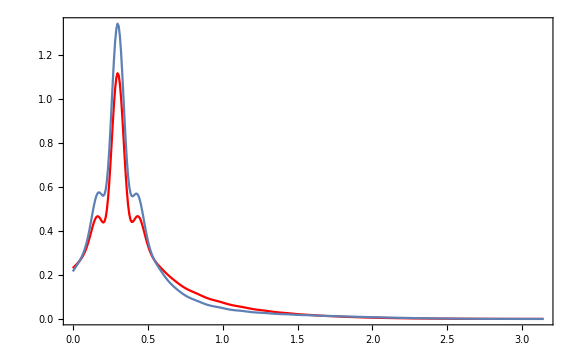

```mathematica
Show[sumV40,sumV4,PlotRange->All]
```

```mathematica
argV4={{#1,g@Arg@#3}&@@@dataV3,ReplaceParams[0.99,-1,#1,1,0.4]@{l,g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ4]]}&@@@dataV4}//ListPlot[#,Joined->False,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Medium]&;
diffV4=ReplaceParams[0.8,-1,#1,1,0.3]@{#1,g@Arg@#3-g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ4]]//Abs}&@@@dataV4//ListLogPlot[#,Joined->False,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Medium]&;
sumV4={Range[0,Pi,Pi/400],Abs[Total@funcV4[[1;;#]]]^2}ᵀ&/@{12,16,20,24,28,32,36,40}//ListPlot[#,Joined->True,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Large]&;
{{diffV4,argV4},{sumV4,SpanFromLeft}}//Grid
```

-Graphics- | -Graphics-
-Graphics- |

## Export data

```mathematica
Clear[FormatZ,Formatϕ]
FormatZ[ℓ_,𝓂_]:=({#1,#2,-(ω̄ τ^2 Abs[𝒶[0]]^2)/(χ Abs[#3]^2),-1/(1+(ℬ^2 τ^2 Abs[#4]^2)/(4 χ ω̄(τ^2+ 4 χ^2)Abs[𝒶[0]]^2)),(ℬ^2 τ^4)/(4 χ^2 (τ^2+4 χ^2))Abs[#4/#3]^2-1}//ReplaceParams[#1,-1,ℓ,𝓂,#2])&;
Formatϕ[ℓ_,𝓂_]:={#1,#2,Re[#3],Im[#3],Re[#4],Im[#4]}&;
```

```mathematica
Spin=Range[0.01,0.99,0.01]∪{0.995,0.999,0.9995,0.9999};
```

```mathematica
Omega=Function[𝒿,With[{est=Round[(1+√(1-𝒿^2)) 0.6,0.05]},Range[0,est,Round[est/450,0.0005]]]];
OmegaSpread=Function[𝒿,With[{est=Round[(1+√(1-𝒿^2)) 0.6,0.05]},Range[0,est,Round[est/100,0.0005]]]];
OmegaNegativeSpread=Function[𝒿,With[{est=Round[(1+√(1-𝒿^2)) 0.6,0.05]},Range[-est,est,Round[est/200,0.0005]]]];
OmegaDetailed=Function[𝒿,With[{est=Round[(1+√(1-𝒿^2)) 0.6,0.05]},Range[0,First@TakeSmallest[{𝒿,est},1],First@TakeSmallest[{Ceiling[0.01𝒿,0.0001],Round[est/450,0.0005]},1]]]];
```

```mathematica
Table[ExportAllCSV[0.99,1,ℓ,𝓂,{0.3991}&,"precision2",{PrecisionGoal->12,AccuracyGoal->14,WorkingPrecision->MachinePrecision,MaxSteps->Automatic}],{ℓ,1,4},{𝓂,0,ℓ}];
```

Completed precision2 file with (𝓈,ℓ,m)=(1,1,0) for 1 spin(s) in 0h 05m 57s

Completed precision2 file with (𝓈,ℓ,m)=(1,1,1) for 1 spin(s) in 0h 06m 20s

Completed precision2 file with (𝓈,ℓ,m)=(1,2,0) for 1 spin(s) in 0h 05m 15s

Completed precision2 file with (𝓈,ℓ,m)=(1,2,1) for 1 spin(s) in 0h 05m 19s

Completed precision2 file with (𝓈,ℓ,m)=(1,2,2) for 1 spin(s) in 0h 05m 09s

Completed precision2 file with (𝓈,ℓ,m)=(1,3,0) for 1 spin(s) in 0h 05m 28s

Completed precision2 file with (𝓈,ℓ,m)=(1,3,1) for 1 spin(s) in 0h 05m 35s

Completed precision2 file with (𝓈,ℓ,m)=(1,3,2) for 1 spin(s) in 0h 05m 42s

Completed precision2 file with (𝓈,ℓ,m)=(1,3,3) for 1 spin(s) in 0h 05m 27s

Completed precision2 file with (𝓈,ℓ,m)=(1,4,0) for 1 spin(s) in 0h 05m 35s

Completed precision2 file with (𝓈,ℓ,m)=(1,4,1) for 1 spin(s) in 0h 05m 41s

Completed precision2 file with (𝓈,ℓ,m)=(1,4,2) for 1 spin(s) in 0h 05m 36s

Completed precision2 file with (𝓈,ℓ,m)=(1,4,3) for 1 spin(s) in 0h 05m 28s

Completed precision2 file with (𝓈,ℓ,m)=(1,4,4) for 1 spin(s) in 0h 05m 22s

```mathematica
(*ExportAllCSV[0.99,1,1,1,Omega,"test2"]*)
```

```mathematica
(*ExportAllCSV[1,1,1,{0.995,0.999,0.9995,0.9999},Omega,"precision",IncreasePrecision]*)
```

```mathematica
Table[{#3,#5}&@@First@Import@GetZFile[1,ℓ,𝓂,"precision2"],{ℓ,1,4},{𝓂,0,ℓ}]//Column
```

{{-0.943775,-0.943892},{0.0328502,0.0328977}}
{{-0.00153209,-0.00149008},{5.78312×10^-7,0.0000424256},{0.000289971,0.000331642}}
{{-6.12064×10^-8,0.0000418814},{8.11492×10^-12,0.0000418156},{3.25204×10^-8,0.0000417071},{1.41635×10^-6,0.000042993}}
{{-1.12102×10^-12,0.0000421803},{7.07349×10^-17,0.0000417113},{1.49998×10^-12,0.0000417844},{1.87203×10^-10,0.0000416758},{4.30024×10^-9,0.0000417874}}

```mathematica
Table[Divide@@N[{#6^2+#5^2-#3^2-#4^2,#3^2+#4^2},20]&@@First@Import@GetϕFile[1,ℓ,𝓂,"precision2"],{ℓ,1,4},{𝓂,0,ℓ}]
```

{{-0.943892,0.0328977},{-0.00149008,0.0000424256,0.000331642},{0.0000418814,0.0000418156,0.0000417071,0.000042993},{0.0000421803,0.0000417113,0.0000417844,0.0000416758,0.0000417874}}

{𝒶[1]→-((s^2 τ^2+λ τ^2+s τ (τ+ⅈ χ)+ⅈ τ χ+2 χ^2+(-2 ⅈ s τ^2-4 τ χ) ω̄) 𝒶[0])/(τ^2 ((-1+s) τ+2 ⅈ χ)),𝒶[2]→((s^4 τ^4-2 λ τ^4+16) 𝒶[0])/(2 τ^4 ((-2+s) τ+2 ⅈ χ) ((-1+s) τ+2 ⅈ χ)),𝒶[3]→-111/1,1,𝒶[5]→-((s^10 τ^10+64+32 τ^5 (-ⅈ s^5 τ^5+1+5) (ω̄)^5) 𝒶[0])/(120 τ^10 ((-5+s) τ+2 ⅈ χ) (1+1) ((1) τ+2 ⅈ χ) ((-2+s) τ+2 ⅈ χ) ((-1+s) τ+2 ⅈ χ)),𝒶[6]→((1) 𝒶[0])/(720 τ^12 ((-6+s) τ+2 ⅈ χ) ((-5+s) τ+2 ⅈ χ) ((-4+s) τ+2 ⅈ χ) ((-3+s) τ+2 ⅈ χ) ((-2+s) τ+2 ⅈ χ) ((-1+s) τ+2 ⅈ χ))}
 |  |  |  |